## Initialization

Try to model exactly the solution for two cells

```mathematica
Clear["Global`*"];
```

```mathematica
S[x_]:= Coff +(Con-Coff)*x;
g[x1_,x2_]:= S[x1] + fd*S[x2];
RSolve[{x1[t+1] == g[x1[t], x2[t]]^n/(k^n+g[x1[t], x2[t]]^n),x2[t+1] == g[x2[t], x1[t]]^n/(k^n+g[x2[t], x1[t]]^n), x1[0]==x1i, x2[0]==x2i} /. {n-> 1}, {x1[t],x2[t]},t]
```

RSolve[{x1[1+t]==(Coff+(-Coff+Con) x1[t]+fd (Coff+(-Coff+Con) x2[t]))/(Coff+k+(-Coff+Con) x1[t]+fd (Coff+(-Coff+Con) x2[t])),x2[1+t]==(Coff+fd (Coff+(-Coff+Con) x1[t])+(-Coff+Con) x2[t])/(Coff+k+fd (Coff+(-Coff+Con) x1[t])+(-Coff+Con) x2[t]),x1[0]==x1i,x2[0]==x2i},{x1[t],x2[t]},t]

Typical value of f(d):

```mathematica
fdval = Exp[R-a0]/a0 Sinh[R] /. {R-> 0.1, a0-> 1.5}
```

0.0164672

## Numerical solution (dynamics)

We do observe that the two cells approach the same state. But does this hold in general, in all situations? Is the steady state unique or does it depend on initial conditions? Evidence so far suggests it might be unique, but can we prove this?

```mathematica
tmax = 20;
params =  {k-> 18, Coff-> 1, Con-> 26, fd-> fdval, n->2,x1i-> 0.05, x2i-> 0.8};
solvals=RecurrenceTable[{x1[t+1] == g[x1[t], x2[t]]^n/(k^n+g[x1[t], x2[t]]^n),x2[t+1] == g[x2[t], x1[t]]^n/(k^n+g[x2[t], x1[t]]^n), x1[0]==x1i, x2[0]==x2i} /.params, {x1[t],x2[t]},{t,0,tmax}]
```

{{0.05,0.8},{0.0203733,0.577331},{0.00950705,0.424464},{0.00626214,0.294584},{0.00514377,0.17826},{0.00456124,0.0846852},{0.00417407,0.0294496},{0.00394597,0.00941064},{0.00384975,0.00482508},{0.00382038,0.00398587},{0.00381301,0.00384082},{0.00381135,0.00381601},{0.00381099,0.00381178},{0.00381092,0.00381105},{0.00381091,0.00381093},{0.0038109,0.00381091},{0.0038109,0.0038109},{0.0038109,0.0038109},{0.0038109,0.0038109},{0.0038109,0.0038109},{0.0038109,0.0038109}}

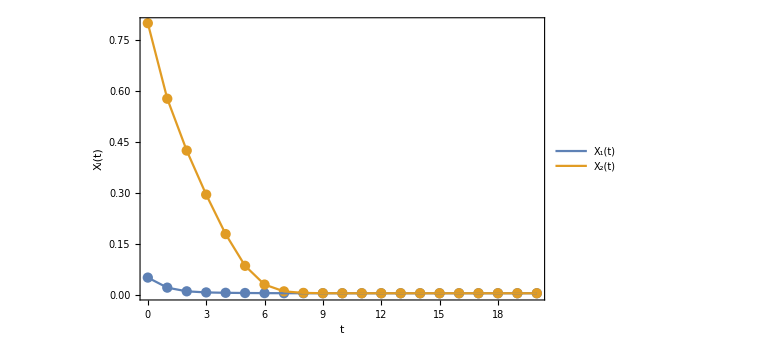

```mathematica
flist = Transpose[{Range[0,tmax], #}] &;
legend = {"X_1(t)","X_2(t)"};
p1=ListPlot[flist/@Transpose[solvals], PlotRange-> All];
p2=ListPlot[flist/@Transpose[solvals], PlotRange-> All, Joined-> True, PlotLegends->Placed[legend, Above]];
fig1=Show[p1,p2,ImageSize-> Large,BaseStyle-> {FontSize-> 20}, Frame-> True, FrameLabel-> {"t", "X_i(t)"}]
```

Export figure

```mathematica
name=  StringReplace["dynamics_k_%1_Coff_1_Con_%2_a0_1p5_R_0p1_n_2_x1i_0p1_x2i_0p8.pdf", {"%1"-> ToString[k /. params], "%2" -> ToString[Con /. params]}];
fname = FileNameJoin[{NotebookDirectory[], "finite_Hill_two_cells", name}];
Export[fname, fig1]
```

H:\My Documents\Multicellular automaton\Mathematica\finite_Hill_two_cells\dynamics_k_18_Coff_1_Con_26_a0_1p5_R_0p1_n_2_x1i_0p1_x2i_0p8.pdf

## Plot vector field of system

```mathematica
S[x_]:= Coff +(Con-Coff)*x;
g[x1_,x2_]:= S[x1] + fd*S[x2];
params = {k-> 18, Coff-> 1, Con->26, fd-> fdval, n->2};
```

Solve for fixed points, find stability

```mathematica
nsol=NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals,0≤ x1 ≤ 1, 0≤ x2 ≤ 1} /. params, {x1,x2}];
J=FullSimplify/@{{D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x1],D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x2]},{ D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x1],D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x2]}};
Jn =FullSimplify[J  /. params];
ev=Table[ Eigenvalues[Jn  /. nsol[[i]]], {i, 1, Length[nsol]}];
Print["Eigenvalues: (λ1, λ2)=", MatrixForm/@ev ];
stability = MapThread[And, Transpose@Negative[ev]];
Print["Eigenvalues positive?"];
TableForm[stability, TableHeadings->{Table[StringReplace["Eigenvector number = %d", "%d" ->  ToString[i]], {i,1,Length[nsol]}], {"Positive?"}}]
```

Eigenvalues: (λ1, λ2)={(-0.832308
-0.826692)}

Eigenvalues positive?

Eigenvector number = 1 | True

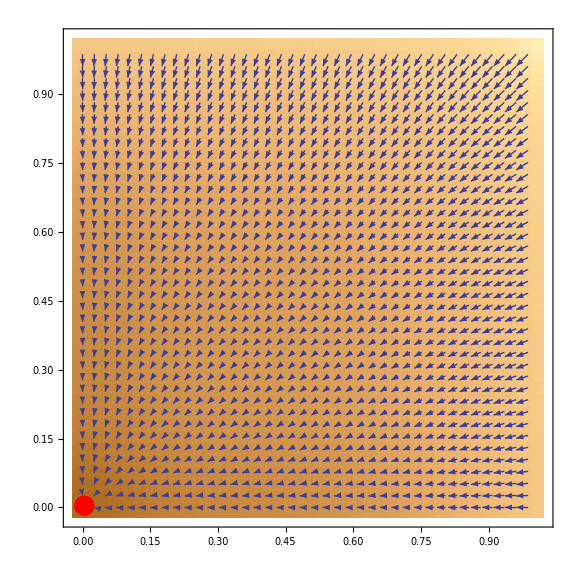

```mathematica
p1=VectorDensityPlot[{g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1, g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2} /. params, {x1,0,1}, {x2,0,1}, VectorPoints-> 40];
p2a=ListPlot[{x1,x2}/.Part[nsol, Pick[Range[Length[ev]], stability]], PlotStyle-> {Red,PointSize[0.025]}];
p2b=ListPlot[{x1,x2}/.Part[nsol, Pick[Range[Length[ev]], Not/@stability]], PlotStyle-> {Green,PointSize[0.025], FaceForm[White]}];
Show[p1,p2a,p2b, ImageSize-> Large]
```

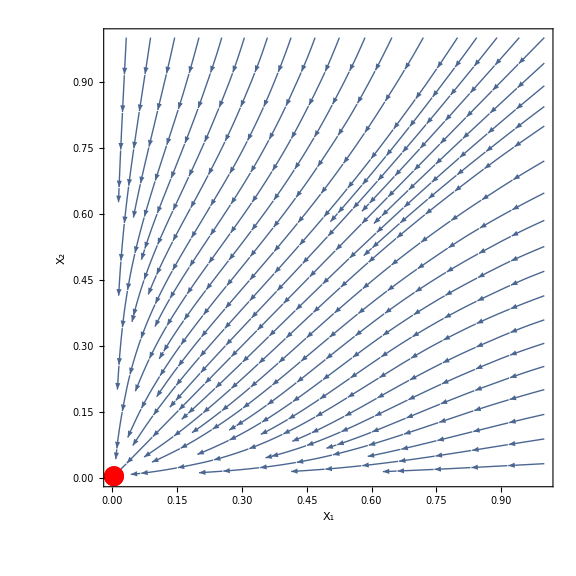

```mathematica
p1b=StreamPlot[{g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1, g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2} /. params, {x1,0,1}, {x2,0,1}];
fig3=Show[p1b,p2a,p2b, BaseStyle-> {FontSize-> 20}, PlotRange-> {{0,1},{0,1}}, FrameLabel-> {"X_1", "X_2"}, ImageSize-> Large]
```

Export figure

```mathematica
name = "vector_field_k_18_Con_21_Coff_1_a0_0p5_R_0p1_n_2.pdf";
fname = FileNameJoin[{NotebookDirectory[], "finite_Hill_two_cells", name}];
Export[fname,fig3]
```

H:\My Documents\Multicellular automaton\Mathematica\finite_Hill_two_cells\vector_field_k_18_Con_21_Coff_1_a0_0p5_R_0p1_n_2.pdf

## Energy functions

Try to obtain a Lyapunov function for this system

```mathematica
params = {k-> 10, Coff-> 1, Con-> 18, fd-> fdval, n-> 2};
nsol=NSolve[{x1sol== g[x1sol, x2sol]^n/(k^n+g[x1sol, x2sol]^n),x2sol == g[x2sol, x1sol]^n/(k^n+g[x2sol, x1sol]^n), x1sol∈ Reals, x2sol∈ Reals} /. params, {x1sol,x2sol}]
```

{{x1sol→0.653724,x2sol→0.653724},{x1sol→0.202489,x2sol→0.202489},{x1sol→0.02614,x2sol→0.02614}}

Try proposed energy function. Does not work.

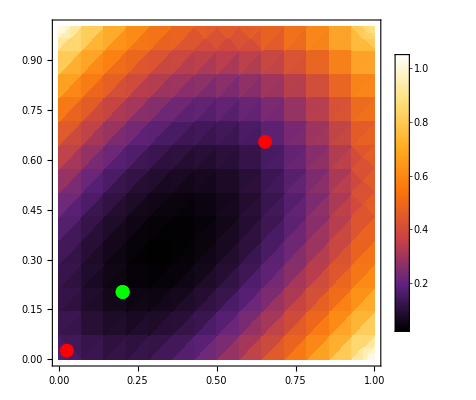

```mathematica
Efunc[x1_,x2_]:= A (x1-x2)^2 + B  Sum[(x1-x1sol)^2(x2-x2sol)^2/.nsol[[i]], {i,{1, 3}}];
p1a=DensityPlot[Efunc[x1,x2] /. {A-> 1, B-> 1}, {x1,0,1}, {x2,0,1}, ColorFunction->"SunsetColors",PlotLegends->Automatic];
p1b=ListPlot[{x1sol,x2sol}/.Part[nsol, {1,3}], PlotStyle-> {Red,PointSize[0.025]}];
p1c=ListPlot[{x1sol,x2sol}/.Part[nsol, {2}], PlotStyle-> {Green,PointSize[0.025], FaceForm[White]}];
Show[p1a,p1b,p1c]
```

Try to match a double well potential (quartic equation) with minima and maxima at the locations of the stable and unstable fixed points respectively. 
Does not work.

```mathematica
Clear[a,b,c,d];
V[x_]:= a x^4+b x^3 + c x^2 + d x + e;
sol=x/.Solve[D[V[x], x]==0, x, Reals];
nsol=Sort[xsol/.Solve[{xsol== g[xsol, xsol]^n/(k^n+g[xsol, xsol]^n), xsol∈Reals}/.params, {xsol}]];
Solve[{nsol[[1]] == sol[[1]], nsol[[2]] == sol[[2]], nsol[[2]] == sol[[2]], Solve[D[V[x], x]]/.{x->0} == -1 }, {a,b,c,d}];
```